I will use double-struck M (𝕄, dsM) to mean a bunch of equations or ODEs.
Units : ω = ℏ = 1 (ω is energy splitting)
Taking Ω∈Real for now. I am using conventions in PvdS where E(t) = E_0cos(ωt), so Ω is the Rabi frequency for population.
Frequency of the drive ν = 1 + DeltaIn

## Two level system

All the calculations below eventually look at the population in one of the state. As we have talked about in the 2025/12/02 meeting, there are some complications if we look at the inner product of the TLS state with some other basis state (in our case, the TLS states are Bloch states ψ_nk, and the “some other basis state” is the plane wave component e^ikx where k is within the first BZ). See photo from the meeting page.

No coherence (our case): we accidentally cancelled out the cross-terms resulting from coherences by doing the opposite shaking, since starting the shake in the opposite direction is the same as adding a π phase shift to the modulation, i.e. Ω→-Ω, resulting in cross-terms with opposite signs. In this case, the inner product differences looks the same as the population plots, but with reduced contrast.

With coherence: no simple relations - we need to also know the inner products explicitly.

## Solving the ODE

### Defining the equations

The original ODE to be solved (in the frame rotating at the frequency of the drive).
Initial conditions listed separately.

```mathematica
𝕄TLSnoRWA={I*c2'[t]==-δ*c2[t]-(Ω/2+Ω/2*Exp[2*I*ν*t])*c1[t],I*c1'[t]==-(Ω/2+Ω/2*Exp[-2*I*ν*t])*c2[t]};
𝕄InitCon={c1[0]==1,c2[0]==0};
```

RWA amounts to setting the counter-rotating terms (terms with ⅇ^(±2ⅈνt)) to zero.

```mathematica
𝕄noRWA=Join[𝕄TLSnoRWA,𝕄InitCon]/.ν->1+δ
𝕄RWA=Join[𝕄TLSnoRWA,𝕄InitCon]/.{Exp[2*I*ν*t]->0,Exp[-2*I*ν*t]->0};
```

{ⅈ c2'[t]==-((Ω/2+1/2 ⅇ^(2 ⅈ t (1+δ)) Ω) c1[t])-δ c2[t],ⅈ c1'[t]==(-Ω/2-1/2 ⅇ^(-2 ⅈ t (1+δ)) Ω) c2[t],c1[0]==1,c2[0]==0}

### Analytic solution

As we have learned in AMO classes, the RWA simplifies the ODE dramatically, and the solution is very simple.
We also see that the equation without the RWA is not easily solvable. This is what makes the RWA so useful.

```mathematica
{c1RWAraw,c2RWAraw}=DSolveValue[𝕄RWA,{c1,c2},t];
DSolveValue[𝕄noRWA,{c1,c2},t](*Doesn't give a solution*)
```

DSolveValue[{ⅈ c2'[t]==-((Ω/2+1/2 ⅇ^(2 ⅈ t (1+δ)) Ω) c1[t])-δ c2[t],ⅈ c1'[t]==(-Ω/2-1/2 ⅇ^(-2 ⅈ t (1+δ)) Ω) c2[t],c1[0]==1,c2[0]==0},{c1,c2},t]

```mathematica
c1RWA=Function[{t},Evaluate[FullSimplify[c1RWAraw[[2]]]]];
c2RWA=Function[{t},Evaluate[FullSimplify[c2RWAraw[[2]]]]];
Ωeffrules={Sqrt[δ^2+Ω^2]->Subscript[Ω, eff],1/Sqrt[δ^2+Ω^2]->1/Subscript[Ω, eff]};(*Just for the TraditionalForm below*)
TraditionalForm[c1RWA/.Ωeffrules]
TraditionalForm[c2RWA/.Ωeffrules]
```

{t}↦ⅇ^((ⅈ δ t)/2) (cos((t Ω_eff)/2)-(ⅈ δ sin((t Ω_eff)/2))/Ω_eff)

{t}↦(ⅈ Ω ⅇ^((ⅈ δ t)/2) sin((t Ω_eff)/2))/Ω_eff

### Parametric numerical solutions

We therefore solve the equations without RWA numerically. We allow the parameters to be specified later.
I cannot “unpack” PrmnoRWA into c1 and c2, which makes sense. They probably have to be solved together.

```mathematica
tMaxPrm=100;
PrmSolnoRWA=ParametricNDSolveValue[𝕄noRWA,{c1,c2},{t,0,tMaxPrm},{Ω∈Reals,δ∈Reals}]
```

ParametricFunction[<>]

Call signature for this ParametricFunction thingy.

```mathematica
PrmSolnoRWA[0.2,-0.3][[2]][20]
```

-0.146622+0.281751 ⅈ

## Plots

Quick visualization of time evolution.
Very roughly we get minimum population in the ground band after 1ms of shaking for 10.8 kHz f_mod. This roughly corresponds to Ω=0.05*2π. I might want to take the moving average to account for the small range of t_mod we use.

```mathematica
Manipulate[ParamList={Ω->OmegaIn,δ->DeltaIn};
tmax=Min[(20/Ω)/.ParamList,tMaxPrm];
Plot[{Abs[c1RWA[t]/.ParamList]^2,Abs[PrmSolnoRWA[OmegaIn,DeltaIn][[1]][t]]^2},{t,0,tmax},PlotRange->{0,1}],{{DeltaIn,0},-0.9,0.9},{{OmegaIn,0.05*2*Pi},0.01,2}]
```

Plot::plln: Limiting value Min[63.662, tMaxPrm] in 
    {t, 0, Min[63.662, tMaxPrm]} is not a machine-sized real number.

Final population in the ground state as a function of δ and Ω after a fixed evolution time (chosen to be half of a Rabi cycle). I’ll pick a few Ω’s while treating δ as the variable. We see that

it is at least roughly monotonic on either side of the minimum. Far off resonance it still looks somewhat like a sinc.

it is almost at its minimum on resonance, although the quick-oscillating term broadens the feature a lot and slightly redshifts it

Longer and weaker modulation is better, if we can tolerate it - both better frequency resolution and less counter-rotating artifacts. In practice we are limited by hole dynamics.

```mathematica
(*Define a function that makes the plot for a given Ω0*)
makePlot[ω0_]:=Module[{t0=Pi/ω0},Plot[{Abs[c1RWA[t0]/. Ω->ω0]^2,Abs[PrmSolnoRWA[ω0,δ][[1]][t0]]^2},{δ,-0.8,0.8},PlotLegends->Placed[{"RWA","no RWA"},{Right,Bottom}],PlotRange->{0,1},PlotLabel->Row[{"Ω₀ = ",ω0/(2 Pi)," × 2π"}],AxesLabel->{"δ",None}]];
```

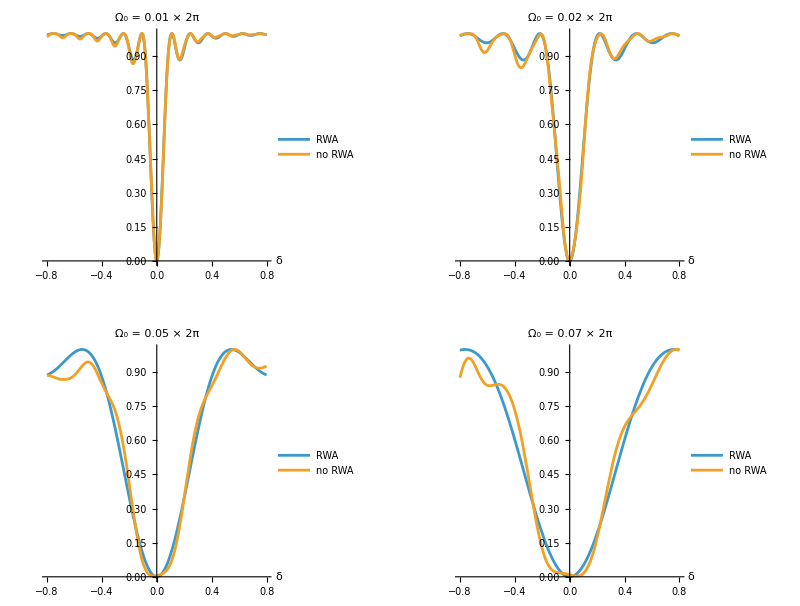

```mathematica
omegas={0.01,0.02,0.05,0.07}*2*Pi;(*The values of Ω0 you want to scan*)
(*Generate all plots and arrange them nicely*)
plots=makePlot/@omegas;
GraphicsGrid[Partition[plots,2]]
```

Plot::sclfn: The scaling function quadratic cannot be used to scale coordinates.

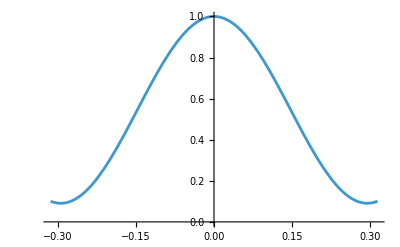

```mathematica
Plot[Abs[PrmSolnoRWA[Ω*2*Pi,0][[1]][1]]^2,{Ω,-0.05*2*Pi,0.05*2*Pi},ScalingFunctions->"quadratic"]
```